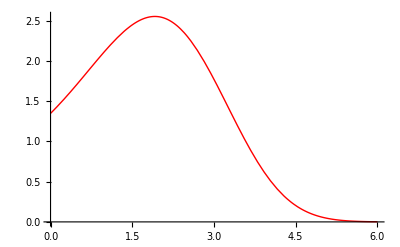

```mathematica
f[x_]=√3*Exp[-1/22* x^3+1/2*x-1/4];
a=0;b=6;n1=6;n2=10;x0=2.4316;h1=(b-a)/n1;h2=(b-a)/n2;
graph=Plot[f[x],{x,a,b},PlotStyle->{Red,Thick}]
```

```mathematica
data1=Table[{i h1,f[i h1]},{i,0,n1}]//N;
data2=Table[{i h2,f[i h2]},{i,0,n2}]//N;
```

```mathematica
{TableForm[data1],TableForm[data2]}
```

{0. | 1.34892
1. | 2.12517
2. | 2.54892
3. | 1.77187
4. | 0.543468
5. | 0.0559939
6. | 0.00147533,0. | 1.34892
0.6 | 1.80306
1.2 | 2.27223
1.8 | 2.54522
2.4 | 2.38916
3. | 1.77187
3.6 | 0.978807
4.2 | 0.379717
4.8 | 0.0975292
5.4 | 0.0156365
6. | 0.00147533}

```mathematica
(*a*)
Pl1[x_]=∏_(i=0)^n1 (x-data1[[i+1,1]])
```

(-6.+x) (-5.+x) (-4.+x) (-3.+x) (-2.+x) (-1.+x) (0.+x)

```mathematica
Pl2[x_]=∏_(i=0)^n2 (x-data2[[i+1,1]])
```

(-6.+x) (-5.4+x) (-4.8+x) (-4.2+x) (-3.6+x) (-3.+x) (-2.4+x) (-1.8+x) (-1.2+x) (-0.6+x) (0.+x)

```mathematica
Ln1[x_]=Sum[data1[[i+1,2]] Pl1[x]/((x-data1[[i+1,1]]) Pl1'[data1[[i+1,1]]]),{i,0,n1}]//Simplify
```

1.34892+0.170641 x+1.16154 x^2-0.631411 x^3+0.0697816 x^4+0.00679391 x^5-0.00109457 x^6

```mathematica
Ln2[x_]=Sum[data2[[i+1,2]] Pl2[x]/((x-data2[[i+1,1]]) Pl2'[data2[[i+1,1]]]),{i,0,n2}]//Simplify
```

1.34892+0.59014 x+0.533464 x^2-0.638119 x^3+0.469139 x^4-0.212124 x^5+0.0289678 x^6+0.00865659 x^7-0.00349156 x^8+0.000438572 x^9-0.000019431 x^10

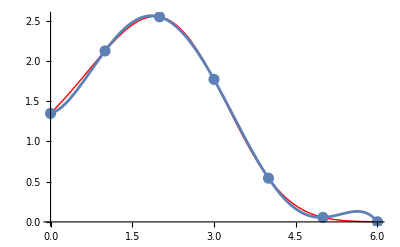

```mathematica
graph1D=ListPlot[data1,PlotStyle->{Darker,PointSize[0.02]}];
graph1Ln=Plot[Ln1[x],{x,a,b}];
Show[graph,graph1D,graph1Ln]
```

```mathematica
graph2D=ListPlot[data2,PlotStyle->{Darker,PointSize[0.02]}];
graph2Ln=Plot[Ln2[x],{x,a,b}];
Show[graph,graph2D,graph2Ln]
```

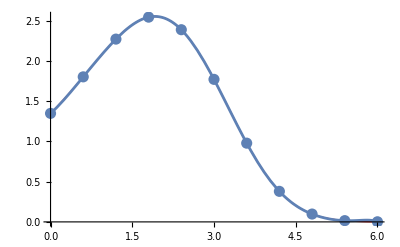

```mathematica
(*б
n=6
*)
```

```mathematica
diftab1=Array[dif1,{n1+1,n1+1},{0,0}];
(*Поскольку с увеличением порядка конечных разностей их количество уменьшается,заполним пустые клетки таблицы:*)
For[k=1,k≤n1,k++,For[i=n1,i≥n1-k,i--,dif1[i,k]=""]];
For[i=0,i≤n1,i++,dif1[i,0]=data1[[i+1,2]]];
For[k=1,k≤n1,k++,For[i=0,i≤n1-k,i++,dif1[i,k]=dif1[i+1,k-1]-dif1[i,k-1]]];
PaddedForm[TableForm[diftab1],{n1,n1-1}]
```

1.34892 |  0.77625 | -0.35250 | -0.84831 |  1.59777 | -1.15496 | -0.78809
 2.12517 |  0.42375 | -1.20080 |  0.74946 |  0.44281 | -1.94305 | 
 2.54892 | -0.77705 | -0.45134 |  1.19227 | -1.50024 |  | 
 1.77187 | -1.22840 |  0.74092 | -0.30797 |  |  | 
 0.54347 | -0.48747 |  0.43296 |  |  |  | 
 0.05599 | -0.05452 |  |  |  |  | 
 0.00148 |  |  |  |  |  |

```mathematica
(*n=10*)
diftab2=Array[dif2,{n2+1,n2+1},{0,0}];
```

```mathematica
For[k=1,k≤n2,k++,For[i=n2,i≥n2-k,i--,dif2[i,k]=""]];
```

```mathematica
For[i=0,i≤n2,i++,dif2[i,0]=data2[[i+1,2]]];
For[k=1,k≤n2,k++,For[i=0,i≤n2-k,i++,dif2[i,k]=dif2[i+1,k-1]-dif2[i,k-1]]];
PaddedForm[TableForm[diftab2],{n2,n2-1}]
```

1.348922525 |  0.454142417 |  0.015020282 | -0.211195342 | -0.021670917 |  0.222336916 | -0.105325470 | -0.245106668 |  0.497902097 | -0.314744326 | -0.426355300
 1.803064942 |  0.469162698 | -0.196175061 | -0.232866259 |  0.200665999 |  0.117011445 | -0.350432139 |  0.252795429 |  0.183157771 | -0.741099626 | 
 2.272227641 |  0.272987638 | -0.429041320 | -0.032200261 |  0.317677444 | -0.233420693 | -0.097636710 |  0.435953200 | -0.557941854 |  | 
 2.545215279 | -0.156053682 | -0.461241581 |  0.285477184 |  0.084256751 | -0.331057403 |  0.338316490 | -0.121988654 |  |  | 
 2.389161597 | -0.617295263 | -0.175764397 |  0.369733934 | -0.246800652 |  0.007259087 |  0.216327836 |  |  |  | 
 1.771866334 | -0.793059660 |  0.193969537 |  0.122933282 | -0.239541566 |  0.223586922 |  |  |  |  | 
 0.978806674 | -0.599090122 |  0.316902820 | -0.116608283 | -0.015954643 |  |  |  |  |  | 
 0.379716552 | -0.282187302 |  0.200294536 | -0.132562927 |  |  |  |  |  |  | 
 0.097529250 | -0.081892766 |  0.067731610 |  |  |  |  |  |  |  | 
 0.015636484 | -0.014161157 |  |  |  |  |  |  |  |  | 
 0.001475327 |  |  |  |  |  |  |  |  |  |

```mathematica
(*в*)
(*Построим вторые интерполяционные многочлены Ньютона Pn1(x) и Pn2(x) для n1=6 и n2=10:*)
q1=(x-b)/h1;Pn1[x_]=dif1[n1,0];P1[q_]=1;
For[k=1,k≤n1,k++,P1[q_]=P1[q1]*(q1+k-1);Pn1[x_]=Pn1[x]+dif1[n1-k,k]/(k!) P1[q1]]
```

```mathematica
Pn1[x]//Simplify
```

1.34892+0.170641 x+1.16154 x^2-0.631411 x^3+0.0697816 x^4+0.00679391 x^5-0.00109457 x^6

```mathematica
q2=(x-b)/h2;Pn2[x_]=dif2[n2,0];P2[q_]=1;
```

```mathematica
For[k=1,k≤n2,k++,P2[q_]=P2[q2]*(q2+k-1);Pn2[x_]=Pn2[x]+dif2[n2-k,k]/(k!) P2[q2]];
```

```mathematica
Pn2[x]//Simplify
```

1.34892+0.59014 x+0.533464 x^2-0.638119 x^3+0.469139 x^4-0.212124 x^5+0.0289678 x^6+0.00865659 x^7-0.00349156 x^8+0.000438572 x^9-0.000019431 x^10

```mathematica
(*Второй интерполяционный многочлен Ньютона n=6*)
graph1Pn=Plot[Pn1[x],{x,a,b}];
Show[graph,graph1D,graph1Pn]
```

-Graphics-

```mathematica
(*Второй интерполяционный многочлен Ньютона для n=10:*)
graph2Pn=Plot[Pn2[x],{x,a,b}];
Show[graph,graph2D,graph2Pn]
```

-Graphics-

```mathematica
(*г*)
(*Интерполяционные многочлены Ньютона функции f(x) для n1=6 и n2=10,построенные встроенной функцией пакета Mathematica:*)
Npn1[x_]=InterpolatingPolynomial[data1,x]//Simplify
```

1.34892+0.170641 x+1.16154 x^2-0.631411 x^3+0.0697816 x^4+0.00679391 x^5-0.00109457 x^6

```mathematica
Npn2[x_]=InterpolatingPolynomial[data2,x]//Simplify
```

1.34892+0.59014 x+0.533464 x^2-0.638119 x^3+0.469139 x^4-0.212124 x^5+0.0289678 x^6+0.00865659 x^7-0.00349156 x^8+0.000438572 x^9-0.000019431 x^10

```mathematica
(*Изобразим полученные интерполяционные многочлены. Интерполяционный многочлен Ньютона для n=6:*)
```

```mathematica
graph1Npn=Plot[Npn1[x],{x,a,b}];
Show[graph,graph1D,graph1Npn]
```

-Graphics-

```mathematica
(*Интерполяционный многочлен Ньютона для n=10:*)
```

```mathematica
graph2Npn=Plot[Npn2[x],{x,a,b}];
Show[graph,graph2D,graph2Npn]
```

-Graphics-

```mathematica
(*д*)
(*Значения интерполяционных многочленов Лагранжа в точке x0:*)
Print["Ln1[x0]=",Ln1[x0],", Ln2[x0]=",Ln2[x0]]
```

Ln1[x0]=2.34451, Ln2[x0]=2.36689

```mathematica
(*Значения вторых интерполяционных многочленов Ньютона в точке x0:*)
Print["Pn1[x0]=",Pn1[x0],", Pn2[x0]=",Pn2[x0]]
```

Pn1[x0]=2.34451, Pn2[x0]=2.36689

```mathematica
(*Значения интерполяционных многочленов Ньютона в точке x0:*)
Print["Npn1[x0]=",Npn1[x0],", Npn2[x0]=",Npn2[x0]]
```

Npn1[x0]=2.34451, Npn2[x0]=2.36689

```mathematica
(*Исходя из полученных графиков и значений в точке x0,отметим,что интерполяционные многочлены,полученные различными способами,совпадают полностью*)
```

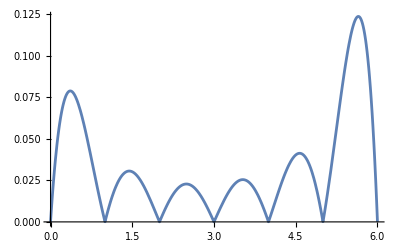

```mathematica
(*е*)
(*Исследуем погрешность интерполирования многочленом Ньютона при n=6.*)
Rn1[x_]=Abs[f[x]-Npn1[x]];
(*График погрешности Rn1(x):*)
graphErr1=Plot[Rn1[x],{x,a,b},PlotRange->Full]
```

```mathematica
maxErr1=FindMaximum[Rn1[x],{x,a,b}]
```

{0.0788952,{x→0.362669}}

```mathematica
(*Как видно из графика,максимальная погрешность интерполирования многочленом Ньютона при n=6 принадлежит отрезку x ϵ[5.2;6].В силу погрешности машинного сравнения рациональных чисел функцияFindMaximumдала некорректный ответ.
Для получения более точного результата сузим промежуток значений аргумента:.*)
maxErr1=FindMaximum[Rn1[x],{x,5.2,b}]
```

{0.12377,{x→5.64942}}

```mathematica
Rn2[x_]=Abs[f[x]-Npn2[x]];
(*График погрешности Rn2(x):*)
```

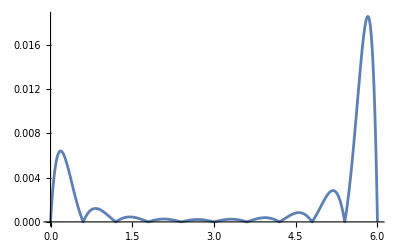

```mathematica
graphErr2=Plot[Rn2[x],{x,a,b},PlotRange->Full]
```

```mathematica
maxErr2=FindMaximum[Rn2[x],{x,a,b}]
```

{0.00640436,{x→0.185113}}

```mathematica
(*Как видно из графика,максимальная погрешность интерполирования многочленом Ньютона при n=10 принадлежит отрезку x ϵ[5.4;6].В силу погрешности машинного сравнения рациональных чисел функцияFindMaximumдала некорректный ответ.Для получения более точного результата сузим промежуток значений аргумента:*)
```

```mathematica
maxErr2=FindMaximum[Rn2[x],{x,5.4,b}]
```

{0.0185618,{x→5.82374}}

```mathematica
(*ж*)
(*Исходя из полученных графиков погрешностей,можно сделать вывод,что с увеличением степени интерполяционного многочлена n погрешность интерполирования уменьшается (значение maxErr1 больше значения maxErr2).*)
```